# MQγ

## 01) Constantes M, Q, γ, y Función Lapsus Horizontes: f(r,M, Q, γ). Gráfico

### 1. Constantes M, Q, γ.

```mathematica
M0=1;
Q0=0.8;
γ0=0.08;
L0=1;
```

### 2. Función Lapsus, derivada y polinomio de los horizontes: f (r, M, Q, γ). Gráfico

```mathematica
f[r_,M_,Q_,γ_]=Collect[1-(2*M)/r+Q^2/r^2-γ*r,r]
fp[r_,M_,Q_,γ_]=D[f[r,M,Q,γ], r]
PH[r_,M_,Q_,γ_]=Collect[-r^2/γ*(f[r,M,Q,γ]),r]
PE[r_,M_,Q_,γ_]=Collect[-r^3/γ*(fp[r,M,Q,γ]),r]
```

1+Q^2/r^2-(2 M)/r-r γ

-(2 Q^2)/r^3+(2 M)/r^2-γ

r^3-Q^2/γ+(2 M r)/γ-r^2/γ

r^3+(2 Q^2)/γ-(2 M r)/γ

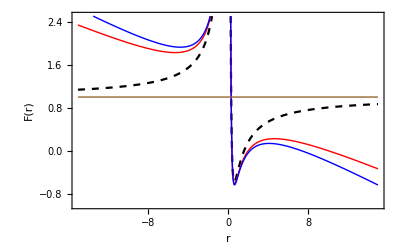

```mathematica
Plot[{f[r,M0,Q0,0],f[r,M0,Q0,γ0],f[r,M0,Q0,0.1],1},{r,-15,15},PlotStyle->{{Black,Dashed},{Red,Thick},{Blue,Thick},{Brown,Thick},{Black,Thick,Dashed},{Purple,Thick},{Orange,Thick}},PlotRange->{-1,2.5},Frame->True,FrameLabel->{Style["r",Bold],Style["F(r) ",Bold]}]
```

```mathematica
NSolve[f[r,M0,Q0,0]==0,r]
```

{{r→1.6},{r→0.4}}

```mathematica
NSolve[f[r,M0,Q0,γ0]==0,r]
```

{{r→10.1041},{r→2.},{r→0.395878}}

### 3. Agujero Extremo 1 (tres iguales r_- = r_+ = r_++)

```mathematica
Collect[(r-H)^3,r]
```

-H^3+3 H^2 r-3 H r^2+r^3

```mathematica
γC=N[1/6]
```

0.166667

```mathematica
QC=N[2*√3/3]
```

1.1547

```mathematica
rC=2;
```

```mathematica
NSolve[f[r,M0,QC,γC]==0,r]
```

{{r→2.},{r→2.},{r→2.}}

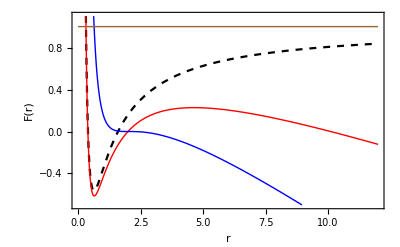

```mathematica
Plot[{f[r,M0,Q0,0],f[r,M0,Q0,γ0],f[r,M0,QC,γC],1},{r,0,12},PlotStyle->{{Black,Dashed},{Red,Thick},{Blue,Thick},{Brown,Thick},{Black,Thick,Dashed},{Purple,Thick},{Orange,Thick}},PlotRange->{-0.7,1.1},Frame->True,FrameLabel->{Style["r",Bold],Style["F(r) ",Bold]}]
```

### 4. Agujero Extremo 2 (dos iguales: r_+ = r_++)

```mathematica
Solve[f[r,M,Q,γ]==0,r];
```

```mathematica
Δ[M_,Q_,γ_]=Collect[1/γ^2*(4 (-1+6 M γ)^3+(-2+18 M γ-27 Q^2 γ^2)^2),γ]
```

-108 M^2+108 Q^2+(864 M^3-972 M Q^2) γ+729 Q^4 γ^2

```mathematica
NSolve[Δ[M0,Q0,γ]==0,γ]
```

{{γ→-0.947595},{γ→0.137409}}

```mathematica
γC1=0.1374093354286095
```

0.137409

```mathematica
NSolve[f[r,M0,Q0,γC1]==0,r]
```

{{r→3.44222},{r→3.44222},{r→0.393085}}

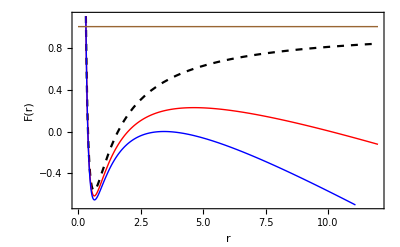

```mathematica
Plot[{f[r,M0,Q0,0],f[r,M0,Q0,γ0],f[r,M0,Q0,γC1],1},{r,0,12},PlotStyle->{{Black,Dashed},{Red,Thick},{Blue,Thick},{Brown,Thick},{Black,Thick,Dashed},{Purple,Thick},{Orange,Thick}},PlotRange->{-0.7,1.1},Frame->True,FrameLabel->{Style["r",Bold],Style["F(r) ",Bold]}]
```

```mathematica
Solve[Δ[M,Q,γ]==0,γ]
```

{{γ→(2 (-8 M^3+9 M Q^2-√(64 M^6-144 M^4 Q^2+108 M^2 Q^4-27 Q^6)))/(27 Q^4)},{γ→(2 (-8 M^3+9 M Q^2+√(64 M^6-144 M^4 Q^2+108 M^2 Q^4-27 Q^6)))/(27 Q^4)}}

```mathematica
γQ[M_,Q_]=(2 (-8 M^3+9 M Q^2+√((4 M^2-3 Q^2)^3)))/(27 Q^4);
```

```mathematica
γQ[M0,Q0]
```

0.137409

### 5. Agujero Extremo 3 (dos iguales: r_- = r_+)

```mathematica
NSolve[Δ[M0,Q,γ0]==0,Q]
```

{{Q→-1.04846},{Q→0.-2.75332 ⅈ},{Q→0.+2.75332 ⅈ},{Q→1.04846}}

```mathematica
QC1=1.0484630100432137;
```

```mathematica
NSolve[f[r,M0,QC1,γ0]==0,r]
```

{{r→10.1759},{r→1.16204},{r→1.16204}}

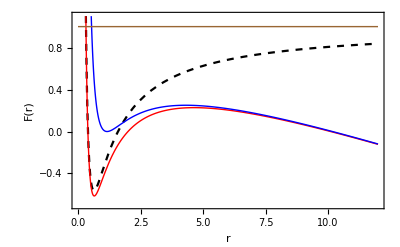

```mathematica
Plot[{f[r,M0,Q0,0],f[r,M0,Q0,γ0],f[r,M0,QC1,γ0],1},{r,0,12},PlotStyle->{{Black,Dashed},{Red,Thick},{Blue,Thick},{Brown,Thick},{Black,Thick,Dashed},{Purple,Thick},{Orange,Thick}},PlotRange->{-0.7,1.1},Frame->True,FrameLabel->{Style["r",Bold],Style["F(r) ",Bold]}]
```

```mathematica
Solve[Δ[M,Q,γ]==0,Q]
```

{{Q→-1/3 √(2/3) √(-1/γ^2+(9 M)/γ-(√(-(-1+6 M γ)^3))/γ^2)},{Q→1/3 √(2/3) √(-1/γ^2+(9 M)/γ-(√(-(-1+6 M γ)^3))/γ^2)},{Q→-1/3 √(2/3) √(-1/γ^2+(9 M)/γ+(√(-(-1+6 M γ)^3))/γ^2)},{Q→1/3 √(2/3) √(-1/γ^2+(9 M)/γ+(√(-(-1+6 M γ)^3))/γ^2)}}

```mathematica
Qγ[M_,γ_]=1/3 √(2/3) √((-1+9 M γ+√(-(-1+6 M γ)^3))/γ^2);
```

```mathematica
Qγ[M0,γ0]
```

1.04846

### 6. Agujeros Extremos. Gráficos 4

```mathematica
NSolve[Δ[M,Q0,γ0]==0,M]
```

{{M→-0.824142},{M→0.772508},{M→1.61413}}

```mathematica
MC1=0.7725078602439156;
MC2=1.6141338933875846;
```

```mathematica
NSolve[f[r,MC1,Q0,γ0]==0,r]
```

{{r→10.7768},{r→0.861588},{r→0.861588}}

```mathematica
NSolve[f[r,MC2,Q0,γ0]==0,r]
```

{{r→6.14404},{r→6.14404},{r→0.211925}}

### 7. Gráfico Función Lapsus: Final

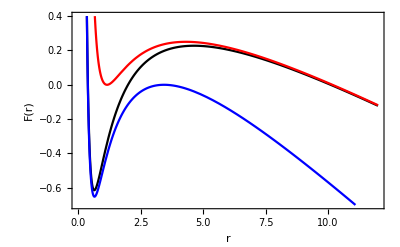

```mathematica
Plot[{f[r,M0,Q0,γ0],f[r,M0,QC1,γ0],f[r,M0,Q0,γC1]},{r,0,12},PlotStyle->{{Black},{Red},{Blue}},PlotRange->{-0.7,0.4},Frame->True,FrameLabel->{Style["r",Bold],Style["F(r) ",Bold]}]
```

### 8. Horizontes: Solución Analítica

```mathematica
PH[r,M,Q,γ]
```

r^3-Q^2/γ+(2 M r)/γ-r^2/γ

```mathematica
PHU[U_,M_,Q_,γ_]=Collect[PH[U+1/(3*γ),M,Q,γ],U]
```

U^3+U (-1/(3 γ^2)+(2 M)/γ)-2/(27 γ^3)+(2 M)/(3 γ^2)-Q^2/γ

```mathematica
χ[M_,γ_]=(2*√(1-6 M γ))/(3*γ);
Ξ[M_,Q_,γ_]=(2-18 M γ+27 Q^2 γ^2)/(2 *√((1-6 M γ)^3));
U[n_,M_,Q_,γ_]=χ[M,γ]*Cos[1/3*ArcCos[Ξ[M,Q,γ]]+(2*n*π)/3];
```

```mathematica
rh1[n_,M_,Q_,γ_]=N[U[n,M,Q,γ]+1/(3*γ)];
```

```mathematica
NSolve[f[r,M0,Q0,γ0]==0,r]
```

{{r→10.1041},{r→2.},{r→0.395878}}

```mathematica
rh1[0,M0,Q0,γ0]
```

10.1041

```mathematica
rh1[1,M0,Q0,γ0]
```

0.395878

```mathematica
rh1[2,M0,Q0,γ0]
```

2.

```mathematica
Cos[4π/3]
Sin[4π/3]
```

-1/2

-(√3)/2

### 9. Horizontes: Solución Analítica para el latex

```mathematica
χ[M_,γ_]=(2*√(1-6 M γ))/(3*γ);
Ξ[M_,Q_,γ_]=(2-18 M γ+27 Q^2 γ^2)/(2 *√((1-6 M γ)^3));
U[n_,M_,Q_,γ_]=χ[M,γ]*Cos[1/3*ArcCos[Ξ[M,Q,γ]]+(2*n*π)/3];
```

```mathematica
rh1[n_,M_,Q_,γ_]=N[U[n,M,Q,γ]+1/(3*γ)];
```

```mathematica
NSolve[f[r,M0,Q0,γ0]==0,r]
```

{{r→10.1041},{r→2.},{r→0.395878}}

```mathematica
rh1[0,M0,Q0,γ0]
```

10.1041

```mathematica
rh1[1,M0,Q0,γ0]
```

0.395878

```mathematica
rh1[2,M0,Q0,γ0]
```

2.

```mathematica
RHH[M_,Q_,γ_]=1/(3*γ)+χ[M,γ]*Cos[1/3*ArcCos[Ξ[M,Q,γ]]];
```

```mathematica
RHH[M0,Q0,γ0]
```

10.1041

```mathematica
RH[M_,Q_,γ_]=1/(3*γ)+χ[M,γ]/2*(√3*Sin[1/3*ArcCos[Ξ[M,Q,γ]]]-Cos[1/3*ArcCos[Ξ[M,Q,γ]]]);
```

```mathematica
RH[M0,Q0,γ0]
```

2.

```mathematica
RC[M_,Q_,γ_]=1/(3*γ)-χ[M,γ]/2*(√3*Sin[1/3*ArcCos[Ξ[M,Q,γ]]]+Cos[1/3*ArcCos[Ξ[M,Q,γ]]]);
```

```mathematica
RC[M0,Q0,γ0]
```

0.395878

### 10. Función Lapsus: Gráficos Definitivos

```mathematica
γC1
```

0.137409

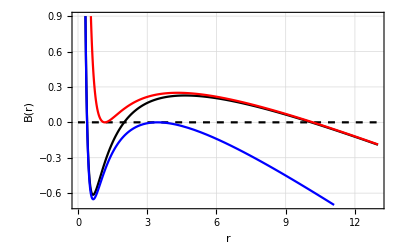

```mathematica
LapsusRNw=Plot[{0,f[r,M0,Q0,γ0],f[r,M0,QC1,γ0],f[r,M0,Q0,γC1]},{r,0,13},PlotStyle->{{Black,Dashed},{Black},{Red},{Blue}},PlotRange->{-0.7,0.9},Frame->True,PlotTheme->"Grid",FrameLabel->{Style["r","Times New Roman",14],Style["B(r)  ","Times New Roman",14]},BaseStyle->{FontFamily->"Times New Roman",12},TicksStyle->Directive[FontFamily->"Times New Roman",12],Epilog->Inset[Framed[Column[{LineLegend[{White,{Black},{Red},{Blue}},{Style["    Q          γ",FontFamily->"Times New Roman"],Style["   0.80      0.08",FontFamily->"Times New Roman"],Style["   1.05      0.08",FontFamily->"Times New Roman"],Style["   0.80      1.14",FontFamily->"Times New Roman"]},LegendMarkerSize->{16,1}]}],RoundingRadius->20],Scaled[{0.8,0.74}]]]
```

```mathematica
Export["LapsusRNw.pdf",LapsusRNw]
```

LapsusRNw.pdf

## 02) Potencial fotones

### a) Definiciones. V(r)

```mathematica
V[r_,M_,Q_,γ_,L_]=Collect[(1-(2*M)/r+Q^2/r^2-γ*r)*L^2/r^2,r]
Vp[r_,M_,Q_,γ_,L_]=D[V[r,M,Q,γ,L], r]
Vpp[r_,M_,Q_,γ_,L_]=D[Vp[r,M,Q,γ,L], r]
```

(L^2 Q^2)/r^4-(2 L^2 M)/r^3+L^2/r^2-(L^2 γ)/r

-(4 L^2 Q^2)/r^5+(6 L^2 M)/r^4-(2 L^2)/r^3+(L^2 γ)/r^2

(20 L^2 Q^2)/r^6-(24 L^2 M)/r^5+(6 L^2)/r^4-(2 L^2 γ)/r^3

### b) Graficos de V(r), graficos para el paper.

```mathematica
rhh=r/.NSolve[f[r,M0,Q0,γ0]==0,r][[1]]
rh=r/.NSolve[f[r,M0,Q0,γ0]==0,r][[2]]
rc=r/.NSolve[f[r,M0,Q0,γ0]==0,r][[3]]
```

10.1041

2.

0.395878

```mathematica
rU3=r/.NSolve[Vp[r,M0,Q0,γ0,1]==0,r][[1]]
rU=r/.NSolve[Vp[r,M0,Q0,γ0,1]==0,r][[2]]
rU1=r/.NSolve[Vp[r,M0,Q0,γ0,1]==0,r][[3]]
```

21.5957

2.89191

0.512386

```mathematica
E2U=V[rU,M0,Q0,γ0,10]
```

1.8365

```mathematica
rI3=r/.NSolve[Vpp[r,M0,Q0,γ0,1]==0,r][[1]]
rI=r/.NSolve[Vpp[r,M0,Q0,γ0,1]==0,r][[2]]
rI1=r/.NSolve[Vpp[r,M0,Q0,γ0,1]==0,r][[3]]
```

33.0323

3.8364

0.631287

```mathematica
E2I=V[rI,M0,Q0,γ0,10]
```

1.4625

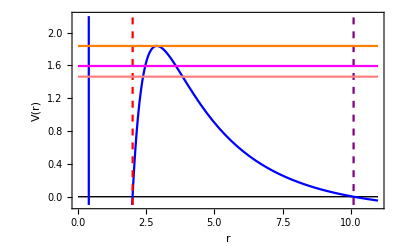

```mathematica
Plot[{0,V[r,M0,Q0,γ0,10],10^5/(r-rh),10^5/(r-rhh),E2I,E2U,ξm^2},{r,0,11},PlotStyle->{{Black,Thin},{Blue},{Red,Dashed},{Purple,Dashed},{Pink},{Orange},{Magenta}},PlotRange->{-0.1,2.2},Frame->True,FrameLabel->{Style["r",Bold],Style["V(r) ",Bold]}]
```

```mathematica
NSolve[Vpp[r,M0,Q0,γ0,1]==0,r]
```

{{r→33.0323},{r→3.8364},{r→0.631287}}

```mathematica
NSolve[V[r,M0,Q0,γ0,10]==E2I,r]
```

{{r→-12.0876},{r→3.8364},{r→2.38548},{r→0.395591}}

```mathematica
N[2.385479015266407/3.836403363810128]
```

0.621801

```mathematica
rF=2.385479015266407;
rf=0.3955906179515069;
```

### c) Circular Inestable: Solución Analítica a r_U

```mathematica
PU[r_,M_,Q_,γ_]=Collect[r^5/(γ*L^2)*(Vp[r,M,Q,γ,L]),r]
```

r^3-(4 Q^2)/γ+(6 M r)/γ-(2 r^2)/γ

```mathematica
PUU[U_,M_,Q_,γ_]=Collect[PU[U+2/(3*γ),M,Q,γ],U]
```

U^3+U (-4/(3 γ^2)+(6 M)/γ)-16/(27 γ^3)+(4 M)/γ^2-(4 Q^2)/γ

```mathematica
12*(16/(27 γ^3)-(4 M)/γ^2+(4 Q^2)/γ)*√(3/(4^3*(4/(3 γ^2)-(6 M)/γ)^3))
```

3/2 √3 √(1/((4/(3 γ^2)-(6 M)/γ)^3)) (16/(27 γ^3)-(4 M)/γ^2+(4 Q^2)/γ)

```mathematica
(√(-γ^6/(-2+9 M γ)^3) (4-27 M γ+27 Q^2 γ^2))/(√2 γ^3)
```

(√(-γ^6/(-2+9 M γ)^3) (4-27 M γ+27 Q^2 γ^2))/(√2 γ^3)

```mathematica
χu[M_,γ_]=(2*√(4-18 M γ))/(3*γ) ;
Ξu[M_,Q_,γ_]=(√2*(4-27M γ+27 Q^2 γ^2))/(2*√((2-9 M γ)^3));
Uu[n_,M_,Q_,γ_]=χu[M,γ]*Cos[1/3*ArcCos[Ξu[M,Q,γ]]+(2*n*π)/3];
```

```mathematica
rUu[n_,M_,Q_,γ_]=N[Uu[n,M,Q,γ]+2/(3*γ)];
```

```mathematica
NSolve[Vp[r,M0,Q0,γ0,1]==0,r]
```

{{r→21.5957},{r→2.89191},{r→0.512386}}

```mathematica
rUu[0,M0,Q0,γ0]
```

21.5957

```mathematica
rUu[1,M0,Q0,γ0]
```

0.512386

```mathematica
rUu[2,M0,Q0,γ0]
```

2.89191

```mathematica
Cos[4π/3]
Sin[4π/3]
```

-1/2

-(√3)/2

### d) Pto de Inflexión: Solución Analítica a r_I

```mathematica
Px[r_,M_,Q_,γ_]=Collect[-r^6/(2*γ*L^2)*(Vpp[r,M,Q,γ,L]),r]
```

r^3-(10 Q^2)/γ+(12 M r)/γ-(3 r^2)/γ

```mathematica
Pxx[U_,M_,Q_,γ_]=Collect[Px[U+1/γ,M,Q,γ],U]
```

U^3+U (-3/γ^2+(12 M)/γ)-2/γ^3+(12 M)/γ^2-(10 Q^2)/γ

```mathematica
(4-16 M γ)/γ^2
```

(4-16 M γ)/γ^2

```mathematica
(√(-γ^6/(-1+4 M γ)^3) (1-6 M γ+5 Q^2 γ^2))/γ^3
```

(√(-γ^6/(-1+4 M γ)^3) (1-6 M γ+5 Q^2 γ^2))/γ^3

```mathematica
χI[M_,γ_]=(2*√(1-4 M γ))/γ ;
ΞI[M_,Q_,γ_]=(1-6M γ+5 Q^2 γ^2)/(√((1-4 M γ)^3));
UI[n_,M_,Q_,γ_]=χI[M,γ]*Cos[1/3*ArcCos[ΞI[M,Q,γ]]+(2*n*π)/3];
```

```mathematica
rII[n_,M_,Q_,γ_]=N[UI[n,M,Q,γ]+1/γ];
```

```mathematica
NSolve[Vpp[r,M0,Q0,γ0,1]==0,r]
```

{{r→33.0323},{r→3.8364},{r→0.631287}}

```mathematica
rII[0,M0,Q0,γ0]
```

33.0323

```mathematica
rII[1,M0,Q0,γ0]
```

0.631287

```mathematica
rII[2,M0,Q0,γ0]
```

3.8364

### razón áurea experimental

```mathematica
φ=N[(√5-1)/2]
```

0.618034

```mathematica
RI[M_,Q_]=M*(φ+2)+√(M^2*(φ+2)^2-Q^2*(φ^2+3*φ+3));
```

```mathematica
RIG=N[RI[M0,Q0]]
```

4.48967

```mathematica
γIG=3/RIG-(12*M0)/RIG^2+(10*Q0^2)/RIG^3
```

0.143597

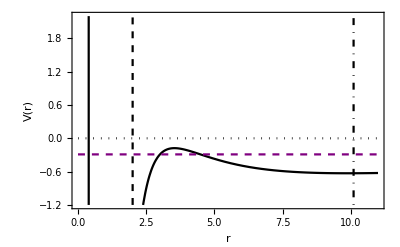

```mathematica
Plot[{0,V[r,M0,Q0,γIG,10],10^5/(r-rh),10^5/(r-rhh),V[RIG,M0,Q0,γIG,10]},{r,0,11},PlotStyle->{{Black,Dotted},{Black},{Black,Dashed},{Black,DotDashed},{Purple,Dashed},{Red,Dashed},{Black,Thin},{Black,Thin}},PlotRange->{-1.2,2.2},Frame->True,FrameLabel->{Style["r",Bold],Style["V(r) ",Bold]}]
```

```mathematica
E2G=V[RIG,M0,Q0,γIG,10]
```

-0.28982

```mathematica
NSolve[V[r,M0,Q0,γIG,10]==E2G,r]
```

{{r→41.659},{r→4.48967},{r→3.00543},{r→0.392845}}

```mathematica
N[3.0054316930507627/4.489669225821957]
```

0.66941

## 3) Geodésicas Nulas

### 1. Puntos de Retorno: Solución Analítica para el latex

```mathematica
Pd[r_,M_,Q_,γ_,L_,ξ_]=Collect[r^4/ξ^2*(ξ^2-V[r,M,Q,γ,L]),r]
```

r^4-(L^2 Q^2)/ξ^2+(2 L^2 M r)/ξ^2-(L^2 r^2)/ξ^2+(L^2 r^3 γ)/ξ^2

```mathematica
Pdd[U_,M_,Q_,γ_,L_,ξ_]=Collect[Pd[U-(γ*L^2)/(4*ξ^2),M,Q,γ,ξ],U]
```

U^4+U^2 (-(3 L^4 γ^2)/(8 ξ^4)-L^2/ξ^2)+U ((L^6 γ^3)/(8 ξ^6)+(L^4 γ)/(2 ξ^4)+(2 L^2 M)/ξ^2)-(3 L^8 γ^4)/(256 ξ^8)-(L^6 γ^2)/(16 ξ^6)-(L^4 M γ)/(2 ξ^4)-(L^2 Q^2)/ξ^2

```mathematica
Ad[γ_,L_,ξ_]=(-(3 L^4 γ^2)/(8 ξ^4)-L^2/ξ^2);
Bd[M_,γ_,L_,ξ_]=((L^6 γ^3)/(8 ξ^6)+(L^4 γ)/(2 ξ^4)+(2 L^2 M)/ξ^2);
Cd[M_,Q_,γ_,L_,ξ_]=(-(3 L^8 γ^4)/(256 ξ^8)-(L^6 γ^2)/(16 ξ^6)-(L^4 M γ)/(2 ξ^4)-(L^2 Q^2)/ξ^2);
```

```mathematica
g2d[M_,Q_,γ_,L_,ξ_]=1/12*(Ad[γ,L,ξ])^2+(Cd[M,Q,γ,L,ξ]);
g3d[M_,Q_,γ_,L_,ξ_]=1/216*(Ad[γ,L,ξ])^3-1/6*(Ad[γ,L,ξ])*(Cd[M,Q,γ,L,ξ])+1/16*(Bd[M,γ,L,ξ])^2;
```

```mathematica
√(g2d[M,Q,γ,L,ξ]/3)
```

(√(1/12 (-(3 L^4 γ^2)/(8 ξ^4)-L^2/ξ^2)^2-(3 L^8 γ^4)/(256 ξ^8)-(L^6 γ^2)/(16 ξ^6)-(L^4 M γ)/(2 ξ^4)-(L^2 Q^2)/ξ^2))/(√3)

```mathematica
1/6 √((L^4-6 L^4 M γ-12 L^2 Q^2 ξ^2)/ξ^4)
```

1/6 √((L^4-6 L^4 M γ-12 L^2 Q^2 ξ^2)/ξ^4)

```mathematica
3*g3d[M,Q,γ,L,ξ]*√(3/(g2d[M,Q,γ,L,ξ])^3)
```

3 √3 (1/216 (-(3 L^4 γ^2)/(8 ξ^4)-L^2/ξ^2)^3+1/16 ((L^6 γ^3)/(8 ξ^6)+(L^4 γ)/(2 ξ^4)+(2 L^2 M)/ξ^2)^2-1/6 (-(3 L^4 γ^2)/(8 ξ^4)-L^2/ξ^2) (-(3 L^8 γ^4)/(256 ξ^8)-(L^6 γ^2)/(16 ξ^6)-(L^4 M γ)/(2 ξ^4)-(L^2 Q^2)/ξ^2)) √(1/((1/12 (-(3 L^4 γ^2)/(8 ξ^4)-L^2/ξ^2)^2-(3 L^8 γ^4)/(256 ξ^8)-(L^6 γ^2)/(16 ξ^6)-(L^4 M γ)/(2 ξ^4)-(L^2 Q^2)/ξ^2)^3))

```mathematica
(L^4 √(-ξ^12/(L^6 (L^2 (-1+6 M γ)+12 Q^2 ξ^2)^3)) (L^2 (-2+18 M γ-27 Q^2 γ^2)+36 (3 M^2-2 Q^2) ξ^2))/(2 ξ^6)
```

(L^4 √(-ξ^12/(L^6 (L^2 (-1+6 M γ)+12 Q^2 ξ^2)^3)) (L^2 (-2+18 M γ-27 Q^2 γ^2)+36 (3 M^2-2 Q^2) ξ^2))/(2 ξ^6)

```mathematica
χd[M_,Q_,γ_,L_,ξ_]=(√(L^4-6 L^4 M γ-12 L^2 Q^2 ξ^2))/(6*ξ^2);
Ξd[M_,Q_,γ_,L_,ξ_]=(L*(-2 L^2+18 L^2 M γ-27 L^2 Q^2 γ^2+108 M^2 ξ^2-72 Q^2 ξ^2))/(2 *√((L^2-6 L^2 M γ-12 Q^2 ξ^2)^3));
Ud[M_,Q_,γ_,L_,ξ_]=χd[M,Q,γ,L,ξ]*Cosh[1/3*ArcCosh[Ξd[M,Q,γ,L,ξ]]];
```

```mathematica
αd[M_,Q_,γ_,L_,ξ_]=Re[√(Ud[M,Q,γ,L,ξ]-Ad[γ,L,ξ]/6)];
βd[M_,Q_,γ_,L_,ξ_]=Re[Ad[γ,L,ξ]/2+2(αd[M,Q,γ,L,ξ])^2+Bd[M,γ,L,ξ]/(4*(αd[M,Q,γ,L,ξ]))];
γd[M_,Q_,γ_,L_,ξ_]=Re[Ad[γ,L,ξ]/2+2(αd[M,Q,γ,L,ξ])^2-Bd[M,γ,L,ξ]/(4*(αd[M,Q,γ,L,ξ]))];
```

```mathematica
re1[M_,Q_,γ_,L_,ξ_]=αd[M,Q,γ,L,ξ]+√((αd[M,Q,γ,L,ξ])^2-βd[M,Q,γ,L,ξ])-(γ*L^2)/(4*ξ^2);
re2[M_,Q_,γ_,L_,ξ_]=αd[M,Q,γ,L,ξ]-√((αd[M,Q,γ,L,ξ])^2-βd[M,Q,γ,L,ξ])-(γ*L^2)/(4*ξ^2);
re3[M_,Q_,γ_,L_,ξ_]=-αd[M,Q,γ,L,ξ]+√((αd[M,Q,γ,L,ξ])^2-γd[M,Q,γ,L,ξ])-(γ*L^2)/(4*ξ^2);
re4[M_,Q_,γ_,L_,ξ_]=-αd[M,Q,γ,L,ξ]-√((αd[M,Q,γ,L,ξ])^2-γd[M,Q,γ,L,ξ])-(γ*L^2)/(4*ξ^2);
```

```mathematica
NSolve[Pd[r,M0,Q0,γ0,10,√E2I]==0,r]
```

{{r→-12.0876},{r→0.395591},{r→2.38548},{r→3.8364}}

```mathematica
N[re1[M0,Q0,γ0,10,√E2I]]
```

3.8364

```mathematica
N[re2[M0,Q0,γ0,10,√E2I]]
```

2.38548

```mathematica
N[re3[M0,Q0,γ0,10,√E2I]]
```

0.395591

```mathematica
N[re4[M0,Q0,γ0,10,√E2I]]
```

-12.0876

```mathematica
-Ad[γ,L,ξ]/6
```

```mathematica
(L^4 γ^2)/(16 ξ^4)+L^2/(6 ξ^2)
```

```mathematica
Ad[γ,L,ξ]/2
```

```mathematica
-(3 L^4 γ^2)/(16 ξ^4)-L^2/(2 ξ^2)
```

```mathematica
Bd[M,γ,L,ξ]/(4*(αd[M,Q,γ,L,ξ]))
```

```mathematica
(L^6 γ^3)/(32 ξ^6)+(L^4 γ)/(8 ξ^4)+(L^2 M)/(2 ξ^2)
```

### 2. Deflección definiciones

```mathematica
rDξ[ξ_]=re1[M0,Q0,γ0,10,ξ];
rFξ[ξ_]=re2[M0,Q0,γ0,10,ξ];
rfξ[ξ_]=re3[M0,Q0,γ0,10,ξ];
r4ξ[ξ_]=re4[M0,Q0,γ0,10,ξ];
```

```mathematica
λ[ξ_]=(rDξ[ξ]-r4ξ[ξ])/(rFξ[ξ]-r4ξ[ξ]);
κ[ξ_]=(√((rDξ[ξ]-rfξ[ξ])*(rFξ[ξ]-r4ξ[ξ])))/(2*(10/ξ));
k[ξ_]=√(((rDξ[ξ]-r4ξ[ξ])/(rFξ[ξ]-r4ξ[ξ]))*((rFξ[ξ]-rfξ[ξ])/(rDξ[ξ]-rfξ[ξ])));
sn[ϕ_,ξ_]=JacobiSN[κ[ξ]*ϕ,k[ξ]];
```

```mathematica
rϕ[ϕ_,ξ_]=Re[(rDξ[ξ]-rFξ[ξ]*λ[ξ]*(sn[ϕ,ξ])^2)/(1-λ[ξ]*(sn[ϕ,ξ])^2)];
```

```mathematica
E2I
E2U
```

1.4625

1.8365

```mathematica
rDξ[√E2I]
```

3.8364

```mathematica
√E2U
```

1.35517

```mathematica
√E2I
```

1.20934

### 3. Ángulo de Deflección

```mathematica
Θ[ξ_]=2/κ[ξ]*(InverseJacobiSN[√(1/λ[ξ]),k[ξ]])-π;
Θp[ξ_]=D[Θ[ξ], ξ];
```

```mathematica
FindRoot[Θp[ξ]==0,{ξ,0.7}]
```

FindRoot[Θp[ξ]==0,{ξ,0.7}]

```mathematica
√E2U
```

1.35517

```mathematica
Θ[0.001]
```

4.94108+0. ⅈ

```mathematica
Θh=Re[Θ[0.001]]
```

4.94108

```mathematica
FindRoot[Θ[ξ]==Θh,{ξ,1.25}]
```

{ξ→1.2619+0. ⅈ}

```mathematica
ξh=Re[1.261903771933251]
```

1.2619

```mathematica
ξm=0.668
```

0.668

```mathematica
ξU=√E2U
```

1.35517

```mathematica
ξI=√E2I
```

1.20934

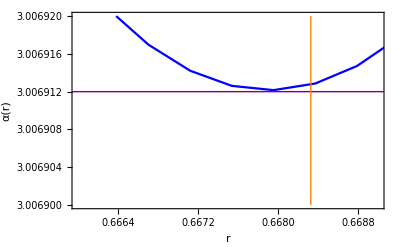

```mathematica
Plot[{Re[Θ[ξ]],10^5/(ξ-√E2U),Re[Θ[0.001]],3.006912,10^5/(ξ-0.668)},{ξ,0.01,1.3552},PlotStyle->{{Blue},{Red,Dashed},{Black,Dashed,Thin},{Purple,Thin},{Orange,Thick}},PlotRange->{{0.666,0.669},{3.0069,3.00692}},Frame->True,FrameLabel->{Style["r",Bold],Style["α(r) ",Bold]}]
```

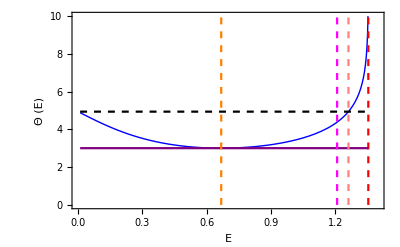

```mathematica
Plot[{Re[Θ[ξ]],10^5/(ξ-√E2U),Re[Θ[0.001]],3.006912,10^5/(ξ-ξm),10^5/(ξ-ξh),10^5/(ξ-√E2I)},{ξ,0.01,1.3552},PlotStyle->{{Blue,Thick},{Red,Dashed},{Black,Dashed},{Purple},{Orange,Dashed},{Pink,Dashed},{Magenta,Dashed}},PlotRange->{{0,1.4},{0,10}},Frame->True,FrameLabel->{Style["E",Bold],Style["Θ (E) ",Bold]}]
```

### 4. Deflección Gráficos: Primera zona

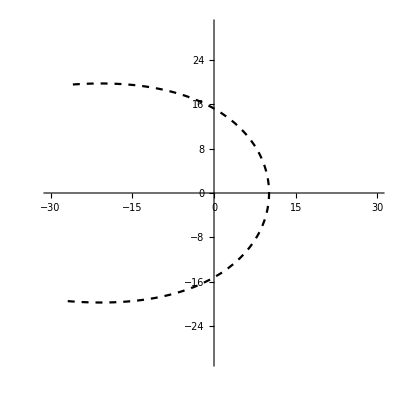

```mathematica
Deflec00=PolarPlot[{rϕ[ϕ,0.001]},{ϕ,-0.8*Pi,0.8*Pi},PlotStyle->{Black,Dashed},PlotRange->{{-30,30},{-30,30}},Epilog->Inset[Framed[Column[{LineLegend[{Red,Blue, Magenta,{Black,Thick,Dotted},{ Magenta,Dashed}},{StringJoin[{"Λ > 0"}],StringJoin[{"Λ = 0"}],StringJoin[{"Λ < 0"}]},LegendMarkerSize->{10,10}]}],RoundingRadius->10],Scaled[{0.22,0.74}]]]
```

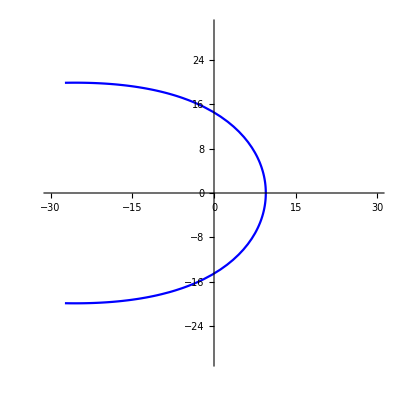

```mathematica
Deflec01=PolarPlot[{rϕ[ϕ,0.2]},{ϕ,-0.8*Pi,0.8*Pi},PlotStyle->{Blue},PlotRange->{{-30,30},{-30,30}},Epilog->Inset[Framed[Column[{LineLegend[{Red,Blue, Magenta,{Black,Thick,Dotted},{ Magenta,Dashed}},{StringJoin[{"Λ > 0"}],StringJoin[{"Λ = 0"}],StringJoin[{"Λ < 0"}]},LegendMarkerSize->{10,10}]}],RoundingRadius->10],Scaled[{0.22,0.74}]]]
```

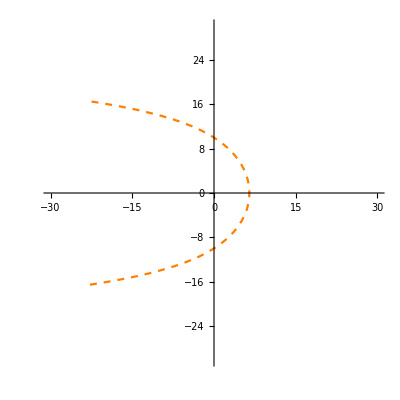

```mathematica
Deflec0m=PolarPlot[{rϕ[ϕ,ξm]},{ϕ,-0.8*Pi,0.8*Pi},PlotStyle->{Orange,Dashed},PlotRange->{{-30,30},{-30,30}},Epilog->Inset[Framed[Column[{LineLegend[{Red,Blue, Magenta,{Black,Thick,Dotted},{ Magenta,Dashed}},{StringJoin[{"Λ > 0"}],StringJoin[{"Λ = 0"}],StringJoin[{"Λ < 0"}]},LegendMarkerSize->{10,10}]}],RoundingRadius->10],Scaled[{0.22,0.74}]]]
```

```mathematica
ξm
```

0.668

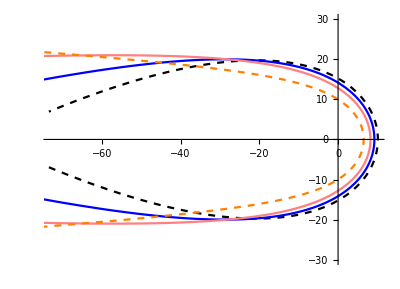

```mathematica
Deflec1P=PolarPlot[{rϕ[ϕ,0.001],rϕ[ϕ,0.25],rϕ[ϕ,0.4],rϕ[ϕ,0.668]},{ϕ,-0.97*Pi,0.97*Pi},PlotStyle->{{Black,Dashed},{Blue},Pink,{Orange,Dashed}},PlotRange->{{-73,10},{-30,30}}]
```

### 5. Deflección Gráficos: Segunda zona

```mathematica
ξm
ξI
ξh
```

0.668

1.20934

1.2619

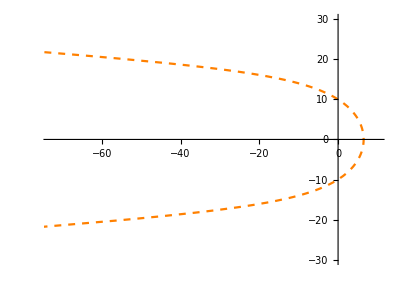

```mathematica
Deflec2P0=PolarPlot[{rϕ[ϕ,0.668]},{ϕ,-0.97*Pi,0.97*Pi},PlotStyle->{{Orange,Dashed},Red,Magenta,{Black,DotDashed}},PlotRange->{{-73,10},{-30,30}}]
```

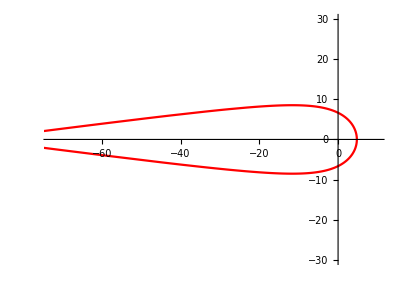

```mathematica
Deflec2P1=PolarPlot[{rϕ[ϕ,1]},{ϕ,-0.999*Pi,0.999*Pi},PlotStyle->{Red},PlotRange->{{-73,10},{-30,30}}]
```

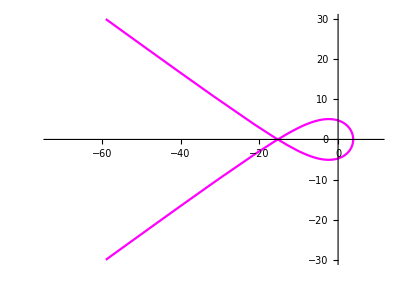

```mathematica
Deflec2P2=PolarPlot[{rϕ[ϕ,ξI]},{ϕ,-1.15*Pi,1.15*Pi},PlotStyle->{Magenta},PlotRange->{{-73,10},{-30,30}}]
```

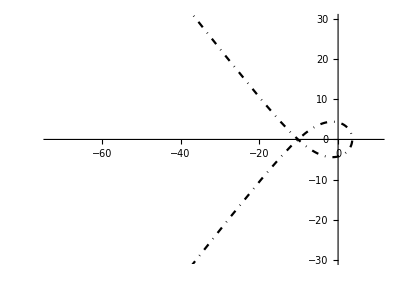

```mathematica
Deflec2P3=PolarPlot[{rϕ[ϕ,ξh]},{ϕ,-1.25*Pi,1.25*Pi},PlotStyle->{{Black,DotDashed}},PlotRange->{{-73,10},{-30,30}}]
```

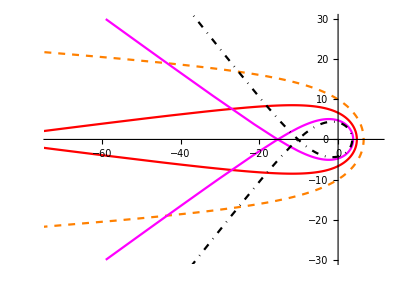

```mathematica
Show[Deflec2P0,Deflec2P1,Deflec2P2,Deflec2P3]
```

### 6. Deflección Gráficos: Tercera zona

```mathematica
ξI
```

1.20934

```mathematica
ξU
```

1.35517

```mathematica
Deflec3P0=PolarPlot[{rϕ[ϕ,ξh]},{ϕ,-1.25*Pi,1.25*Pi},PlotStyle->{{Black,DotDashed}},PlotRange->{{-73,10},{-30,30}}]
```

-Graphics-

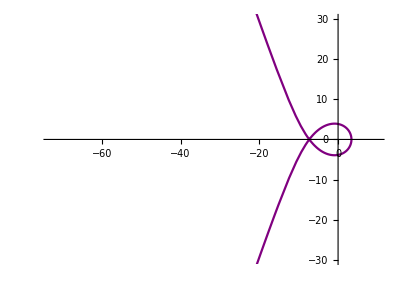

```mathematica
Deflec3P1=PolarPlot[{rϕ[ϕ,1.3]},{ϕ,-1.32*Pi,1.32*Pi},PlotStyle->{{Purple}},PlotRange->{{-73,10},{-30,30}}]
```

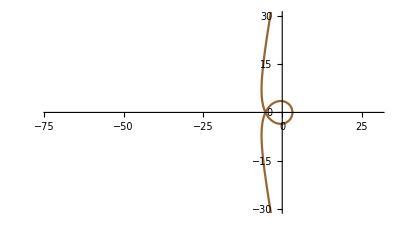

```mathematica
Deflec3P2=PolarPlot[{rϕ[ϕ,1.33]},{ϕ,-1.5*Pi,1.5*Pi},PlotStyle->{{Brown}},PlotRange->{{-73,30},{-30,30}}]
```

```mathematica
ξU
```

1.35517

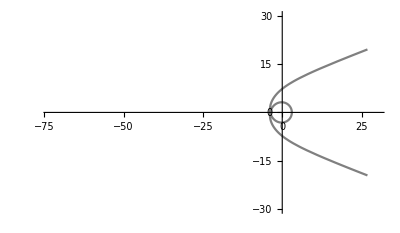

```mathematica
Deflec3P3=PolarPlot[{rϕ[ϕ,1.35]},{ϕ,-1.8*Pi,1.8*Pi},PlotStyle->{{Gray}},PlotRange->{{-73,30},{-30,30}}]
```

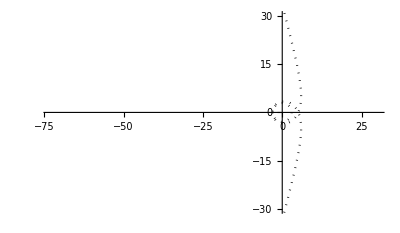

```mathematica
Deflec3P4=PolarPlot[{rϕ[ϕ,1.355]},{ϕ,-2.5*Pi,2.5*Pi},PlotStyle->{{Black,Dotted}},PlotRange->{{-73,30},{-30,30}}]
```

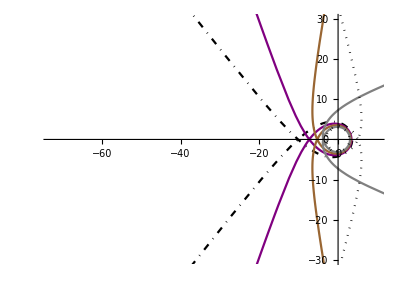

```mathematica
Show[Deflec3P0,Deflec3P1,Deflec3P2,Deflec3P3,Deflec3P4]
```

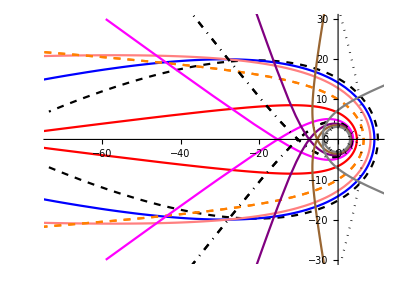

```mathematica
Show[Deflec1P,Deflec2P0,Deflec2P1,Deflec2P2,Deflec2P3,Deflec3P0,Deflec3P1,Deflec3P2,Deflec3P3,Deflec3P4]
```

### 7. Geodésicas de 2.baclase

```mathematica
λ2[ξ_]=(rFξ[ξ]-rfξ[ξ])/(rDξ[ξ]-rfξ[ξ]);
κ[ξ_]=(√((rDξ[ξ]-rfξ[ξ])*(rFξ[ξ]-r4ξ[ξ])))/(2*(10/ξ));
k[ξ_]=√(((rDξ[ξ]-r4ξ[ξ])/(rFξ[ξ]-r4ξ[ξ]))*((rFξ[ξ]-rfξ[ξ])/(rDξ[ξ]-rfξ[ξ])));
sn[ϕ_,ξ_]=JacobiSN[κ[ξ]*ϕ,k[ξ]];
```

```mathematica
r2ϕ[ϕ_,ξ_]=Re[(rFξ[ξ]-rDξ[ξ]*λ2[ξ]*(sn[ϕ,ξ])^2)/(1-λ2[ξ]*(sn[ϕ,ξ])^2)];
```

### 8. Geodésicas de 2.baclase. Gráficos

```mathematica
rU
```

2.89191

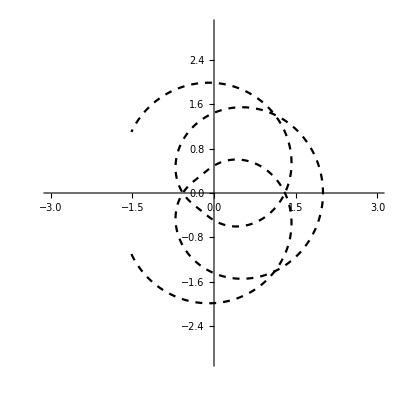

```mathematica
segclase00=PolarPlot[{r2ϕ[ϕ,0.001]},{ϕ,-2.8*Pi,2.8*Pi},PlotStyle->{Black,Dashed},PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
ξU
```

1.35517

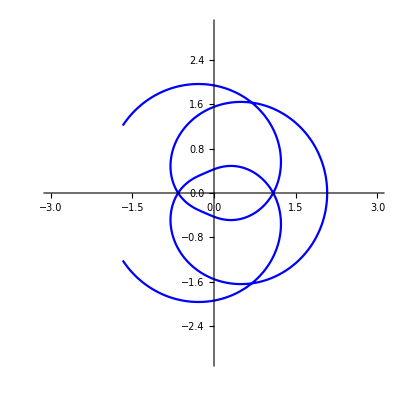

```mathematica
segclase01=PolarPlot[{r2ϕ[ϕ,0.668]},{ϕ,-2.8*Pi,2.8*Pi},PlotStyle->{Blue},PlotRange->{{-3,3},{-3,3}}]
```

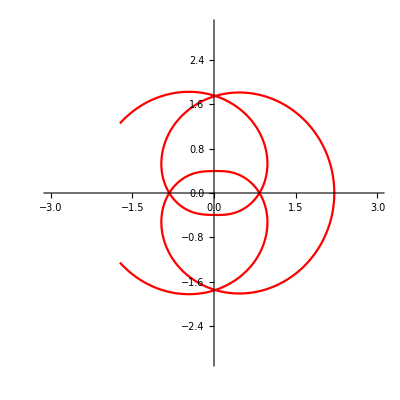

```mathematica
segclase02=PolarPlot[{r2ϕ[ϕ,1]},{ϕ,-2.8*Pi,2.8*Pi},PlotStyle->{Red},PlotRange->{{-3,3},{-3,3}}]
```

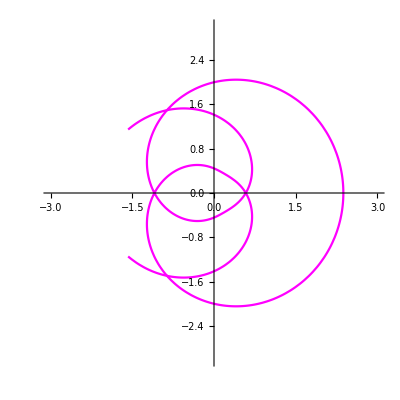

```mathematica
segclase03=PolarPlot[{r2ϕ[ϕ,1.2]},{ϕ,-2.8*Pi,2.8*Pi},PlotStyle->{Magenta},PlotRange->{{-3,3},{-3,3}}]
```

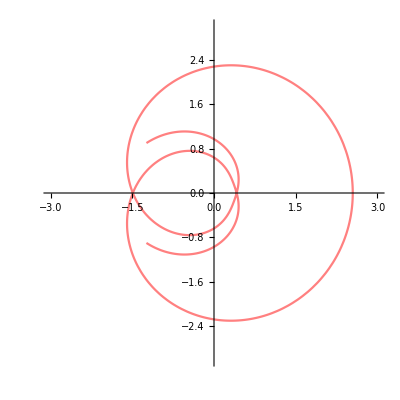

```mathematica
segclase04=PolarPlot[{r2ϕ[ϕ,1.3]},{ϕ,-2.8*Pi,2.8*Pi},PlotStyle->{Pink},PlotRange->{{-3,3},{-3,3}}]
```

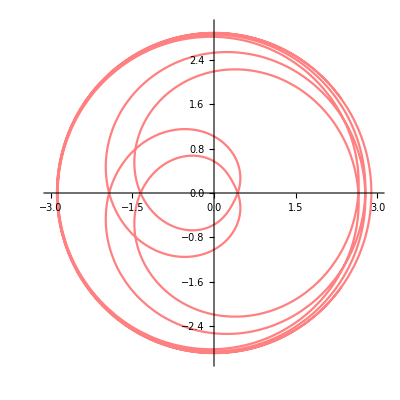

```mathematica
segclase0U=PolarPlot[{r2ϕ[ϕ,1.35517]},{ϕ,-7.8*Pi,7.8*Pi},PlotStyle->{Pink},PlotRange->{{-3,3},{-3,3}}]
```

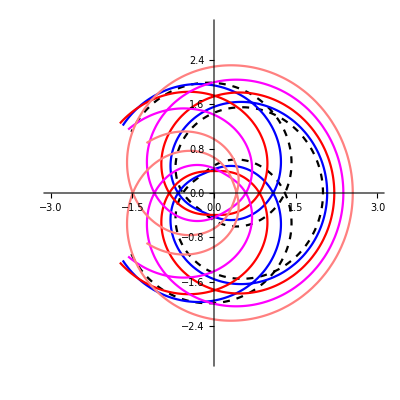

```mathematica
Show[segclase00,segclase01,segclase02,segclase03,segclase04]
```

### 9. Definiciones Zona de Captura

```mathematica
rDξ[2]
rFξ[2]
rfξ[2]
r4ξ[2]
```

2.20476+1.04421 ⅈ

2.20476-1.04421 ⅈ

0.395096

-6.80461

```mathematica
A1[ξ_]=√((rfξ[ξ]-(rDξ[ξ]+rFξ[ξ])/2)^2-1/4*(rDξ[ξ]-rFξ[ξ])^2);
B1[ξ_]=√((r4ξ[ξ]-(rDξ[ξ]+rFξ[ξ])/2)^2-1/4*(rDξ[ξ]-rFξ[ξ])^2);
κ1[ξ_]=(√((A1[ξ])*(B1[ξ])))/(10/ξ);
k1[ξ_]=√(((A1[ξ]+B1[ξ])^2-(rfξ[ξ]-r4ξ[ξ])^2)/(4*(A1[ξ])*(B1[ξ])));
cn[ϕ_,ξ_]=JacobiCN[κ1[ξ]*ϕ,k1[ξ]];
```

```mathematica
Rϕ[ϕ_,ξ_]=Re[(A1[ξ]*r4ξ[ξ]-B1[ξ]*rfξ[ξ]-(A1[ξ]*r4ξ[ξ]+B1[ξ]*rfξ[ξ])*(cn[ϕ,ξ]))/(A1[ξ]-B1[ξ]-(A1[ξ]+B1[ξ])*(cn[ϕ,ξ]))];
```

### 10. Gráficos: Zona de Captura

```mathematica
rfξ[2]
```

0.395096

```mathematica
Rϕ[10,2]
```

4.74889

```mathematica
ξU
```

1.35517

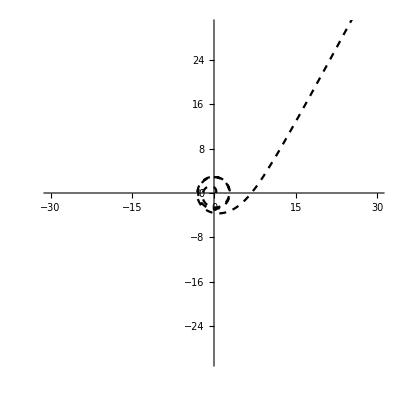

```mathematica
Captura00=PolarPlot[{Rϕ[ϕ,1.3552]},{ϕ,0,6.3*Pi},PlotStyle->{Black,Dashed},PlotRange->{{-30,30},{-30,30}}]
```

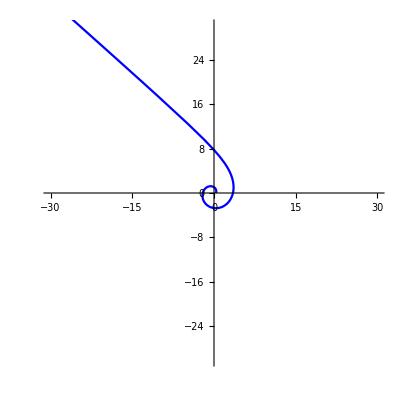

```mathematica
Captura01=PolarPlot[{Rϕ[ϕ,1.5]},{ϕ,0,2.73*Pi},PlotStyle->{Blue},PlotRange->{{-30,30},{-30,30}}]
```

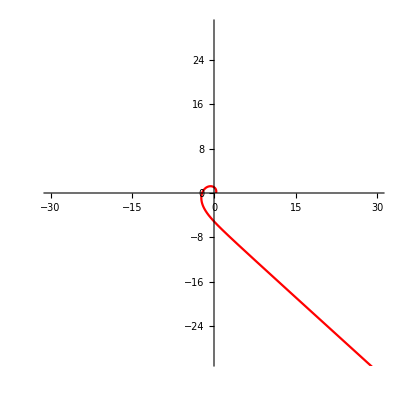

```mathematica
Captura02=PolarPlot[{Rϕ[ϕ,2.5]},{ϕ,0,1.75*Pi},PlotStyle->{Red},PlotRange->{{-30,30},{-30,30}}]
```

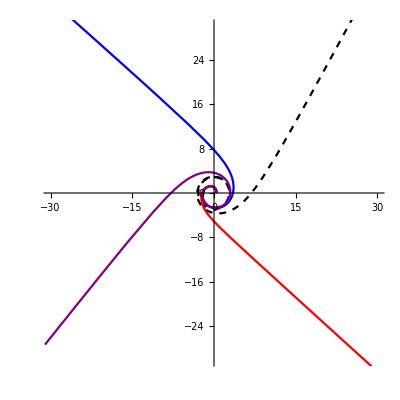

```mathematica
Show[Captura00,Captura01,Captura02,Captura05]
```

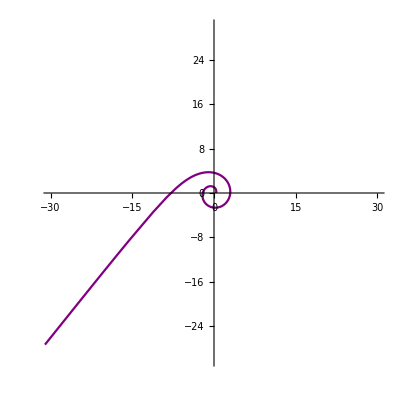

```mathematica
Captura05=PolarPlot[{Rϕ[ϕ,1.4]},{ϕ,0,3.23*Pi},PlotStyle->{Purple},PlotRange->{{-30,30},{-30,30}}]
```

### 11. Crítica 1 clase + gráfico

```mathematica
rDξ[ξU]
rFξ[ξU]
rfξ[ξU]
r4ξ[ξU]
```

2.89191

2.89191

0.395517

-10.5355

```mathematica
δ1[ξ_]=ArcCosh[(2*rDξ[ξ]-rfξ[ξ]-r4ξ[ξ])/(rfξ[ξ]-r4ξ[ξ])];
κc[ξ_]=(√((rDξ[ξ]-rfξ[ξ])*(rDξ[ξ]-r4ξ[ξ])))/(10/ξ);
rc1[ϕ_,ξ_]=Re[rDξ[ξ]+(2*(rDξ[ξ]-rfξ[ξ])*(rDξ[ξ]-r4ξ[ξ]))/((rfξ[ξ]-r4ξ[ξ])*(Cosh[κc[ξ]*ϕ+δ1[ξ]])-(2*rDξ[ξ]-rfξ[ξ]-r4ξ[ξ]))];
```

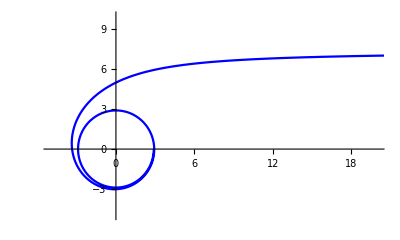

```mathematica
Critica01=PolarPlot[{rc1[ϕ,ξU]},{ϕ,0.2,4*Pi},PlotStyle->{Blue},PlotRange->{{-5,20},{-5,10}}]
```

```mathematica
rc2[ϕ_,ξ_]=Re[rDξ[ξ]-(2*(rDξ[ξ]-rfξ[ξ])*(rDξ[ξ]-r4ξ[ξ]))/((rfξ[ξ]-r4ξ[ξ])*(Cosh[κc[ξ]*ϕ])+(2*rDξ[ξ]-rfξ[ξ]-r4ξ[ξ]))];
```

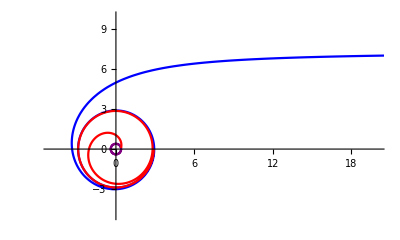

```mathematica
Critica02=PolarPlot[{rfξ[ξU],rc1[ϕ,ξU],rc2[ϕ,ξU]},{ϕ,0.2,4*Pi},PlotStyle->{Purple,Blue,Red},PlotRange->{{-5,20},{-5,10}}]
```

### 12. Radiales + gráfico

```mathematica
Apart[r^2/((H-r)*(r-h)*(r-c)),r]
```

-c^2/((c-h) (c-H) (-c+r))+h^2/((c-h) (h-H) (-h+r))+H^2/((c-H) (-h+H) (-H+r))

```mathematica
hH=rh1[0,M0,Q0,γ0]
```

10.1041

```mathematica
hc=rh1[1,M0,Q0,γ0]
```

0.395878

```mathematica
hh=rh1[2,M0,Q0,γ0]
```

2.

```mathematica
Ah=hH^2/((hH-hh)*(hH-hc));
Bh=hh^2/((hH-hh)*(hh-hc));
Ch=-hc^2/((hH-hc)*(hH-hc));
```

```mathematica
r0=5;
```

```mathematica
te[r_]=-Ah*Log[(hH-r)/(hH-r0)]+Bh*Log[(r-hh)/(r0-hh)]+Ch*Log[(r-hc)/(r0-hc)];
```

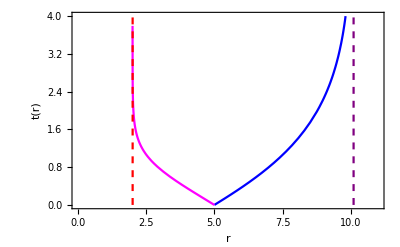

```mathematica
Plot[{te[r],-te[r],10^5/(r-rh),10^5/(r-rhh)},{r,0,11},PlotStyle->{{Blue},{Magenta},{Red,Dashed},{Purple,Dashed},{Pink},{Orange}},PlotRange->{0,4},Frame->True,FrameLabel->{Style["r",Bold],Style["t(r) ",Bold]}]
```